# N-Dimensional universal estimator using DNN

#### New-Logistic function:

The New-Logistic function, σ(x), also defined in (-∞, ∞) and yields values in (0, 1) , but the its central shifts to x=a:

```mathematica
NewSigmoid[x_,a_]:=1/(1+ⅇ^(-x+a))
```

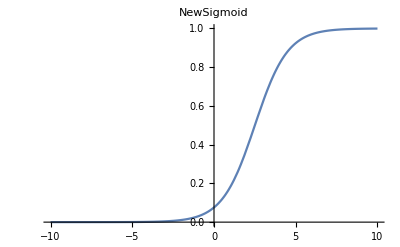

```mathematica
Plot[NewSigmoid[x,2.5], {x, -10, 10}, PlotLabel->HoldForm[NewSigmoid]]
```

#### New - Logit function

```mathematica
NewLogit[x_,a_]:= Log[x/(1-x)]+a
```

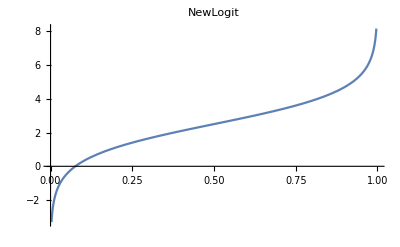

```mathematica
Plot[NewLogit[x,2.5], {x, 0, 1}, PlotLabel->HoldForm[NewLogit]]
```

#### New Range Adjuster

```mathematica
NewAdjuster[low_, high_,a_]:=With[{LOW=NewSigmoid[low,a],HIGH=NewSigmoid[high,a]}, Function[{t},NewLogit[LOW+t(HIGH-LOW),a]]]
```

Given a single parameter a=5 we want to centralize:

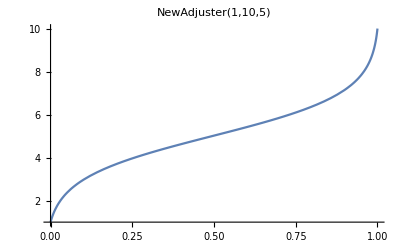

```mathematica
Plot[NewAdjuster[1,10,5][x], {x, 0, 1}, PlotLabel->HoldForm[NewAdjuster[1,10,5]]]
```

## Generating data

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples: 
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, f_, ranges_, a_, bins_:-1]:= 
Module[{nParams, adjusters, params,samples, nbins},
(*a helper function for 1d dimension case if needed*)
Params[params_]:= If[Length[params]>1, params, params[[1]]];
(*number of group of parameters*)
nParams=Dimensions[ranges][[1]];
(*generate an adapter for each parameter range*)
adjusters=Table[NewAdjuster[ranges[[i,1]],ranges[[i,2]], a[[i]]],{i,1,nParams}];
(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,M},{j,1,nParams}];
(*generate M samples from the parameters*)
samples=Table[f[Params@params[[i]],n],{i,1,M}];
(*create a histogram from each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];
(*output*)
Table[h@samples[[i]]->Params@ params[[i]], {i, 1, M}]
]
```

### Example of generated data

```mathematica
(*YuleSimon[{α_,β_}, n_]:=RandomVariate[WaringYuleDistribution[α,β],n];
YuleSimonRanges = {{2,3},{0,10}};
YuleSimonCenter ={2.5,5};

YuleSimonData = GenerateData[20,10,YuleSimon, YuleSimonRanges, YuleSimonCenter];
Print[YuleSimonData//TableForm];*)
```

{1,6,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0}→{2.06257,8.18842}
{1,4,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.69622,5.77681}
{0,2,2,0,3,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.01181,5.5029}
{6,2,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.2528,3.48068}
{3,2,1,1,2,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.93899,6.18529}
{3,1,2,1,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.04047,8.05656}
{7,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.06899,1.69343}
{2,3,0,3,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.78098,4.45528}
{3,2,2,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.79199,5.47295}
{1,1,1,2,1,1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}→{2.44609,6.06128}
{3,0,2,0,1,1,0,0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.79477,6.56698}
{5,2,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.81884,5.35951}
{3,2,0,1,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.23601,3.77875}
{3,0,3,1,1,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.18107,7.52681}
{5,2,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.80997,2.99071}
{7,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.47043,3.88682}
{4,2,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}→{2.07516,5.04156}
{3,3,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}→{2.71305,4.5711}
{7,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.4076,1.70841}
{4,1,1,1,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{2.45236,2.97842}

## DNN

```mathematica
CreateNet[bins_, nParams_]:=( 
NetChain[{
LinearLayer[bins], 
ElementwiseLayer[Ramp], 
LinearLayer[bins], 
ElementwiseLayer[Ramp], 
LinearLayer[bins], 
ElementwiseLayer[Ramp], 
LinearLayer[nParams]},
"Input"->bins, 
"Output" -> If[nParams>1,nParams,"Scalar"]]
)
```

## Adapt the definition of N dimensional distribution generator (Need to define the n dimensional distribution here)

```mathematica
TwodimDist[dist_,θ_]:=dist[θ[[1]],θ[[2]]];
ThreedimDist[dist_,θ_]:=dist[θ[[1]],θ[[2]],θ[[3]]];
```

## N dimension universal estimator

Given a distribution  dist(x|θ) and the range for the parameters θ,  
UniversalEstimator returns an Estimator function for predicting the parameters θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_, a_]:=Module[{g, M, n, trainSet, bins, valSet ,net, trained, model, h, nParams},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[TwodimDist[dist,θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 10000; 
n = 1024;   (*number of observations in each sample*)
trainSet=GenerateData[M,n, g, range, a];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, g, range, a, bins];
nParams=Dimensions[range][[1]];
(*Create and train the NN*)
net = NetInitialize@CreateNet[bins,nParams];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->256
 
];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=HistogramList[x,{0,bins,1}][[2]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of N dimensional universal estimator with DNN

n : number of samples drawn for  given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_, a_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, crb,Var},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range, a];
(*define the size of the test set*)
M = 20;
n = 1024;

Θ=Table[a,M]; (*create M distributions of parameter a*)
	
g[θ_,m_] := RandomVariate[TwodimDist[dist,θ],m];

samples = Table[g[Θ[[i]], n], {i,1,M,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M,1 }];
(*Compute Cramer-Rao bound at a*)
(*crb = CRB[dist, a, n];*)
(*evaluate prediction errors*)
e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M,1 }];
(*Compute the varience of each Subscript[θ, i]*)
(*Var = Mean[e^2];*)

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
(*Print["Variance for θ:",Var];*)
(*Print["crb for θ:",crb];*)
(*Print["ratio of variance and crb for θ:",Var/crb];*)
(*Print["RMSE:",RootMeanSquare[e]];*)

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for different distributions

### Yule-Simon distribution

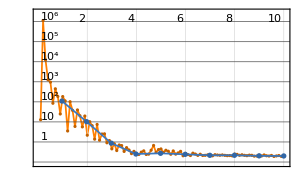
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:100  rounds:10  time:7.1min  examples/s:241
data | ,,  training examples:10000  validation examples:5000  processed examples:102400  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:2.04×10^-1
validation | ,,  loss:2.01×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {{2.5,5},{2.5,5},{2.5,5},{2.5,5},{2.5,5},{2.5,5},{2.5,5},{2.5,5},{2.5,5},{2.5,5}}

θ̂: {{2.75328,5.13818},{2.41033,4.73395},{2.5144,5.26606},{2.48751,4.71075},{2.65688,5.00038},{2.66314,5.26479},{2.68511,5.25663},{2.55472,4.89078},{2.59768,4.94976},{2.55882,4.71206}}

abs(θ-θ̂): {{0.253279,0.138182},{0.0896652,0.266054},{0.014396,0.266057},{0.0124941,0.289246},{0.156885,0.0003829},{0.16314,0.264789},{0.185106,0.256632},{0.054723,0.109222},{0.0976794,0.0502419},{0.0588241,0.287943}}

```mathematica
{Θ, e} = RunExperiment[WaringYuleDistribution, {{2,3},{0,10}},{2.5,5}];
```

### Normal distribution

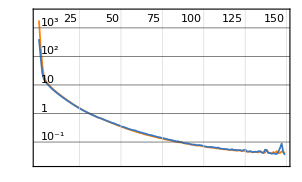
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5960  rounds:149  time:13s  examples/s:123249
data | ,,  training examples:10000  validation examples:5000  processed examples:1525760  skipped examples:0
method | ,,  ADAMoptimizer  batch size256CPU
round | ,,  loss:4.02×10^-2
validation | ,,  loss:3.56×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2},{3,2}}

θ̂: {{3.02654,2.08386},{3.07665,1.98621},{3.01439,1.97676},{3.03392,2.02619},{2.90823,2.20832},{3.15982,2.0392},{3.12378,1.90455},{2.90937,2.18229},{3.08936,1.89578},{3.05428,2.05449},{3.02356,2.0114},{3.04298,2.07342},{2.9999,2.02847},{3.08669,2.08578},{2.91427,2.14457},{3.11647,1.84838},{2.83153,2.08674},{2.93262,2.10235},{3.09911,2.10411},{2.98556,2.21203}}

abs(θ-θ̂): {{0.0265369,0.0838556},{0.0766528,0.0137868},{0.0143948,0.0232446},{0.03392,0.0261874},{0.0917664,0.208317},{0.159817,0.0391991},{0.123783,0.0954549},{0.0906322,0.182293},{0.0893619,0.104225},{0.0542762,0.0544879},{0.0235555,0.0114017},{0.0429819,0.0734169},{0.0000989437,0.0284657},{0.0866892,0.0857844},{0.0857301,0.144575},{0.116466,0.151624},{0.16847,0.0867412},{0.0673807,0.102355},{0.0991135,0.104114},{0.0144351,0.212026}}

```mathematica
{Θ, e} = RunExperiment[NormalDistribution, {{2,4},{1,3}},{3,2}];
```